```mathematica
switch[x_]:=If[x>0,x,0];
ceil[x_,l_Integer]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
```

```mathematica
λ[f_,a_,g_]:=f[#]+a g[#]&
```

```mathematica
legendre[n_,x_]:=LegendreP[n-1,2 x-1] √(2 (n-1)+1)
h[1,1,x_]:=If[Abs[x]>1,0,If[x≥0,1/(√2),-1/(√2)]]
h[2,1,x_]:=If[Abs[x]>1,0,If[x≥0,√(3/2) (-1+2 x),h[2,1,-x]]]
h[2,2,x_]:=If[Abs[x]>1,0,If[x≥0,√(1/2) (-2+3 x),-h[2,2,-x]]]
h[3,1,x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(1/2) (1-24 x+30 x^2),-h[3,1,-x]]]
h[3,2,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(3/2) (3-16 x+15 x^2),h[3,2,-x]]]
h[3,3,x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(5/2) (4-15 x+12 x^2),-h[3,3,-x]]]
h[4,1,x_]:=If[Abs[x]>1,0,If[x≥0, √(15/34) (1+4x-30 x^2+28 x^3),h[4,1,-x]]]
h[4,2,x_]:=If[Abs[x]>1,0,If[x≥0, √(1/42) (-4+105x-300 x^2+210 x^3),-h[4,2,-x]]]
h[4,3,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(35/34) (-5+48x-105 x^2+64 x^3),h[4,3,-x]]]
h[4,4,x_]:=If[Abs[x]>1,0,If[x≥0, 1/2 √(5/42) (-16+105x-192 x^2+105 x^3),-h[4,4,-x]]]
h[5,1,x_]:=If[Abs[x]>1,0,If[x≥0,√(1/186) (1+30x+210 x^2-840 x^3+630 x^4),-h[5,1,-x]]]
h[5,2,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(1/38) (-5-144x+1155 x^2-2240 x^3+1260 x^4),h[5,2,-x]]]
h[5,3,x_]:=If[Abs[x]>1,0,If[x≥0,√(35/14694) (22-735x+3504 x^2-5460 x^3+2700 x^4),-h[5,3,-x]]]
h[5,4,x_]:=If[Abs[x]>1,0,If[x≥0,1/8 √(21/38) (35-512x+1890 x^2-2560 x^3+1155 x^4),h[5,4,-x]]]
h[5,5,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(7/158) (32-315x+960 x^2-1155 x^3+480 x^4),-h[5,5,-x]]]
```

```mathematica
fk[k_,fnumber_]:=h[k,fnumber,#]&
```

```mathematica
vk[k_,fnumber_,level_,place_]:=If[level==0,legendre[fnumber,#1]&,2^(level/2) fk[k,fnumber][2^level #1-(2 place-1)]&]
```

```mathematica
Vk[k_,fnumber_List,level_List,place_List]:=vk[k,fnumber⟦1⟧,level⟦1⟧,place⟦1⟧][#⟦1⟧]vk[k,fnumber⟦2⟧,level⟦2⟧,place⟦2⟧][#⟦2⟧]&
(*Tensor Product Construction*)
```

```mathematica
innerProduct[f_,g_,level_List,place_List,ϵ_]:=(ϵ^2 2^(-switch[level⟦1⟧-1])2^(-switch[level⟦2⟧-1]))Sum[f[{x,y}] g[{x,y}],{x,(place⟦1⟧-1) 2^(-switch[level⟦1⟧-1]),(place⟦1⟧) 2^(-switch[level⟦1⟧-1]),
ϵ 2^(-switch[level⟦1⟧-1])},{y,(place⟦2⟧-1) 2^(-switch[level⟦2⟧-1]),(place⟦2⟧) 2^(-switch[level⟦2⟧-1]),ϵ 2^(-switch[level⟦2⟧-1])}]

innerProduct[f_,g_,level_List,place_List]:=NIntegrate[f[{x,y}] g[{x,y}],{x,(place⟦1⟧-1) 2^(-switch[level⟦1⟧-1]),(place⟦1⟧) 2^(-switch[level⟦1⟧-1])},{y,(place⟦2⟧-1) 2^(-switch[level⟦2⟧-1]),(place⟦2⟧) 2^(-switch[level⟦2⟧-1])},AccuracyGoal->5]
```

### Hierarchical Iteration

```mathematica
hierIterate[k_,n_List,lp_List]:=Module[{fnumber,level,place,hashMap,count},
hashMap=Table[0,{i,1,k 2^n⟦1⟧}];
count=1;
If[Length[n]==1,
For[level=0,level≤n⟦1⟧,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=Join[lp,{fnumber,level+1,place}];
]]];
Return[Partition[Flatten[hashMap],3 Length[n]]];
,
For[level=0,level≤n⟦1⟧,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=hierIterate[k,n⟦2;;⟧,Join[lp,{fnumber,level+1,place}]];
]]];
Return[Partition[Flatten[hashMap],3 Length[n]]];
]
]

hierIterate[k_,n_List]:=hierIterate[k,n,{}]

hierLevFuncIterate[k_,n_List,l_List]:=Module[{count,level,fnumber,hashMap},
If[Length[n]==1,
count=1;
hashMap=Table[0,{i,1,k (n⟦1⟧+1)}];
For[level=0,level≤n⟦1⟧,level++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=Join[l,{fnumber,level+1}];
]];
Return[hashMap];
,
count=1;
hashMap=Table[0,{i,1,k (n⟦1⟧+1)}];
For[level=0,level≤n⟦1⟧,level++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=hierLevFuncIterate[k,n⟦2;;⟧,Join[l,{fnumber,level+1}]];
]];
Return[hashMap]
]
]

hierLevFuncIterate[k_,n_List]:=Partition[Flatten[hierLevFuncIterate[k,n,{}]],2 Length[n]]
```

### Sparse Iteration

```mathematica
sparseIterate[k_,n_,d_,lp_List]:=Module[{fnumber,level,place,hashMap,count},
hashMap=Table[0,{i,1,k 2^n}];
count=1;
If[d==1,
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=Join[lp,{fnumber,level+1,place}];
]]];
Return[hashMap];
,
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=sparseIterate[k,n-level,d-1,Join[lp,{fnumber,level+1,place}]];
]]];
Return[hashMap];
];
]

sparseIterate[k_,n_,d_]:=Partition[Flatten[sparseIterate[k,n,d,{}]],3 d]

sparseLevFuncIterate[k_,n_,d_,l_List]:=Module[{count,level,fnumber,hashMap},
If[d==1,
count=1;
hashMap=Table[0,{i,1,k (n+1)}];
For[level=0,level≤n,level++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=Join[l,{fnumber,level+1}];
]];
Return[hashMap];
,
count=1;
hashMap=Table[0,{i,1,k (n+1)}];
For[level=0,level≤n,level++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧=sparseLevFuncIterate[k,n-level,d-1,Join[l,{fnumber,level+1}]];
]];
Return[hashMap]
]
]

sparseLevFuncIterate[k_,n_,d_]:=Partition[Flatten[sparseLevFuncIterate[k,n,d,{}]],2 d]
```

### Getting the Coefficients

```mathematica
getCoefficientsk[k_,f_,fnumber_List,level_List,place_List]:=innerProduct[f,Vk[k,fnumber,level,place],level,place]
```

```mathematica
sparseCoefficientsk[k_,f_,n_,d_]:=Module[{iters,i,hash,count,coeff},
iters=sparseIterate[k,n,d];
hash=Table[0,{i,1,Length[iters]}];
For[i=1,i≤Length[iters],i++,
coeff=getCoefficientsk[k,f,iters⟦i⟧⟦1;;;;3⟧,iters⟦i⟧⟦2;;;;3⟧-1,iters⟦i⟧⟦3;;;;3⟧];hash⟦i⟧=iters⟦i⟧->coeff;];Return[SparseArray[Chop[hash]]]]
```

```mathematica
pointIndex[x_,l_Integer]:=Module[{},Table[If[k≤1,1,ceil[x,k]],{k,0,l}]]
pointIndex[x_List,l_List]:=Table[pointIndex[x[[i]],l[[i]]],{i,1,Length[l]}]
spointIndex[x_List,n_Integer]:=Table[pointIndex[x⟦i⟧,n],{i,1,Length[x]}]
```

### Reconstruction

```mathematica
sparseReconstructk[k_,coefficients_,x_,n_]:=Module[{a,value,i,d,indices,lp,iters},
value=0;d=Length[x];
indices=spointIndex[x,n];
iters=sparseLevFuncIterate[k,n,d];
For[i=1,i≤Length[iters],i++,
lp=Flatten[Table[{iters⟦i,2a-1⟧,iters⟦i,2a⟧,indices⟦a,iters⟦i,2a⟧⟧},{a,1,d}]];
value+=(coefficients⟦##⟧&@@Sequence[lp])Vk[k,lp⟦1;;;;3⟧,lp⟦2;;;;3⟧-1,lp⟦3;;;;3⟧][x]
];
Return[value];
]
```

```mathematica
scoeffs=sparseCoefficientsk[3,Sin[Pi #[[1]]]&,2,2]
```

SparseArray[<36>, {3, 3, 2, 3, 3, 2}]

```mathematica
Plot3D[sparseReconstructk[3,scoeffs,{x,y},2]-Sin[Pi x],{x,0,1},{y,0,1}]//Timing
```

{3.90204,-Graphics3D-}

```mathematica
Plot3D[{sparseReconstructk[3,scoeffs2,{x,y},2]-Sin[Pi x +y]},{x,0,1},{y,0,1}]//Timing
```

{3.75775,-Graphics3D-}

```mathematica
sparsek2Error2D=Table[Sqrt[.042^2 Sum[(sparseReconstructk[2,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[2,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2],{n,1,4}]
```

{0.0666076,0.0182149,0.00540757,0.00124363}

```mathematica
sparsek3Error2D=Table[Sqrt[.042^2 Sum[(sparseReconstructk[3,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[3,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2],{n,1,4}]
```

{0.00897328,0.00125529,0.000180842,0.0000185444}

```mathematica
sparsek4Error2D=Table[Sqrt[.042^2 Sum[(sparseReconstructk[4,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[4,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2],{n,1,4}]
```

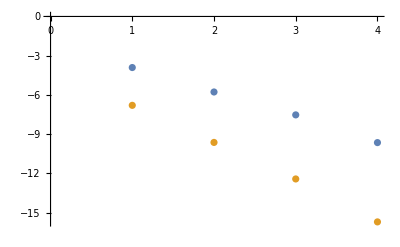

```mathematica
ListPlot[{sparsek2Error2D,sparsek3Error2D}//Log2]
```

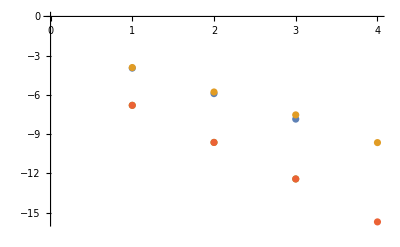

```mathematica
ListPlot[{k2Error2D,sparsek2Error2D,k3Error2D,sparsek3Error2D}//Log2]
```

```mathematica
sparseCoefficientsk[4,Sin[Pi #⟦1⟧+#⟦2⟧]&,3,2]
```

SparseArray[<320>, {4, 4, 4, 4, 4, 4}]

```mathematica
fullCoefficientsk[4,Sin[Pi #⟦1⟧+#⟦2⟧]&,{3,3}]
```

SparseArray[<1010>, {4, 4, 4, 4, 4, 4}]